# AM Final Project

```mathematica
na1dot=α na1 na2
na2dot = -α na1 na2 - r na2 nab - β na2 nb2
nabdot=r na2 nab+s nb2 nab + na2 nb2
nb2dot=-γ nb1 nb2 - s nb2 nab -(1-β)na2  nb2
nb1dot=γ nb1 nb2
β=nb2/(nb2+na2)
```

na1 na2 α

-na2 nab r-na1 na2 α-na2 nb2 β

na2 nb2+na2 nab r+nab nb2 s

-nab nb2 s-na2 nb2 (1-β)-nb1 nb2 γ

nb1 nb2 γ

nb2/(na2+nb2)

```mathematica
nadot=na1dot+na2dot
nabdot
nbdot=nb1dot+nb2dot
```

-(na2 nb2^2)/(na2+nb2)-na2 nab r

na2 nb2+na2 nab r+nab nb2 s

-na2 nb2 (1-nb2/(na2+nb2))-nab nb2 s

```mathematica
nadot+nabdot+nbdot
```

na2 nb2-(na2 nb2^2)/(na2+nb2)-na2 nb2 (1-nb2/(na2+nb2))

```mathematica
Simplify[na2 nb2-na2 nb2 (1-β)-na2 nb2 β]
```

0

```mathematica
na=na1+na2;
nb= nb1+nb2;
nadottwosystem=nadot /. nab->(1-na-nb)
nbdottwosystem=nbdot /. nab->(1-na-nb)
```

-(na2 nb2^2)/(na2+nb2)-na2 (1-na1-na2-nb1-nb2) r

-na2 nb2 (1-nb2/(na2+nb2))-(1-na1-na2-nb1-nb2) nb2 s

```mathematica
Manipulate[StreamPlot[{nadottwosystem/.{na2->na/2, na1->na/2,nb2->nb/2, nb1->nb/2}, nbdottwosystem /.{na2->na/2, na1->na/2,nb2->nb/2, nb1->nb/2}}, {na, 0,1},{nb,0,1}],{r,-1,1}, {s,-1,1}]
```

-(na nb^2)/(4 (na+nb))-1/2 na (1-na-nb) r

-1/4 na nb (1-nb/(na+nb))-1/2 (1-na-nb) nb s

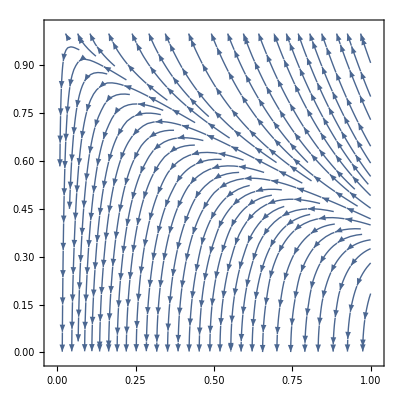

```mathematica
Clear[na, nb]
nadot2=-r na/2 (1-na-nb)-(nb/(na+nb)) na nb/4
nbdot2=-s nb/2 (1-na-nb)-(1-(nb/(na+nb))) na nb/4
StreamPlot[{nadot2/.r->0, nbdot2/.s->1}, {na, 0,1},{nb,0,1}]
```